```mathematica
Table[allGraphs5[k,"comp"]=Equal;allGraphs5[k,"compwhy"]="Ad absurdum";
allGraphs5[k,"atleast"]=0;allGraphs5[k,"atleastwhy"]="Ad absurdum declared to be zero",{k,alfa1s}]
```

{Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero}

```mathematica
PropagateComp[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs5[k];
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs5[leftKey];
right=allGraphs5[rightKey];
If[current["comp"]===GreaterEqual && (left["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from left)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from right)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
current["comp"]=Equal;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];
If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater (right) and zero (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Greater&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Zero (right) and Greater (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===Greater && (left["comp"]===GreaterEqual&&right["comp"]===Equal),
left["compwhy"]="The down relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(right) pushed down to left)";
left["comp"]=Greater;
Print[left["compwhy"]];
changed++;
allGraphs5[children[[1]]]=left;
];

If[current["comp"]===Greater && (left["comp"]===Equal&&right["comp"]===GreaterEqual),
right["compwhy"]="The down relation holds "<> ToString[k]<> "("<> ToString[current["comp"]]<> ") == "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> " (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(left) pushed down to right)";
right["comp"]=Greater;
Print[right["compwhy"]];
changed++;
allGraphs5[children[[2]]]=right;
]
,{children,allGraphs5[k,"children"]}
]
,
{k,Keys[allGraphs5]}],
k
];
changed
]
```

```mathematica
PropagateComp[]
```

The down relation holds 31681(Greater)== 31708(GreaterEqual) + 31738 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 31681(Greater)== 31684(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 31708(Greater)== 31711(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 31465(GreaterEqual)== 31708(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The down relation holds 31465(Greater)== 31468(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 31441(GreaterEqual)== 31684(Greater) + 31954 (GreaterEqual) (greater propagated from left)

The relation holds 27333(GreaterEqual)== 29520(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 27336(GreaterEqual)== 29523(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 27337(GreaterEqual)== 29524(Equal) + 31711 (Greater) (greater propagated from right)

The relation holds 27334(GreaterEqual)== 29521(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 27327(GreaterEqual)== 29514(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 27328(GreaterEqual)== 29515(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 27325(GreaterEqual)== 29512(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 27309(GreaterEqual)== 29496(GreaterEqual) + 31684 (Greater) (greater propagated from right)

The relation holds 27310(GreaterEqual)== 29497(GreaterEqual) + 31684 (Greater) (greater propagated from right)

The relation holds 27255(GreaterEqual)== 29442(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 27256(GreaterEqual)== 29443(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The down relation holds 27259(Greater)== 29446(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 27259(Greater)== 27340(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 27246(GreaterEqual)== 29433(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 27247(GreaterEqual)== 29434(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 26608(GreaterEqual)== 28795(GreaterEqual) + 31711 (Greater) (greater propagated from right)

The relation holds 26605(GreaterEqual)== 28792(GreaterEqual) + 31708 (Greater) (greater propagated from right)

The relation holds 26581(GreaterEqual)== 28768(GreaterEqual) + 31684 (Greater) (greater propagated from right)

The down relation holds 35977(Greater)== 36058(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 35977(Greater)== 36004(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 35326(GreaterEqual)== 36058(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The down relation holds 35326(Greater)== 35353(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 33808(GreaterEqual)== 36004(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The down relation holds 33808(Greater)== 33889(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 33157(GreaterEqual)== 35353(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 22936(GreaterEqual)== 29497(GreaterEqual) + 36058 (Greater) (greater propagated from right)

The down relation holds 23041(Greater)== 29602(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 23041(Greater)== 23044(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 23044(Greater)== 29605(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 22882(GreaterEqual)== 29443(GreaterEqual) + 36004 (Greater) (greater propagated from right)

The relation holds 22873(GreaterEqual)== 29434(GreaterEqual) + 36004 (Greater) (greater propagated from right)

The relation holds 22693(GreaterEqual)== 29254(GreaterEqual) + 36058 (Greater) (greater propagated from right)

The relation holds 22639(GreaterEqual)== 29200(GreaterEqual) + 36004 (Greater) (greater propagated from right)

The relation holds 22207(GreaterEqual)== 28768(GreaterEqual) + 36058 (Greater) (greater propagated from right)

The relation holds 22315(GreaterEqual)== 23044(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 25138(GreaterEqual)== 31708(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The down relation holds 25138(Greater)== 25141(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 24895(GreaterEqual)== 31465(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The down relation holds 24895(Greater)== 24898(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 20776(GreaterEqual)== 27337(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The down relation holds 20803(Greater)== 27364(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 20803(Greater)== 22990(GreaterEqual) + 31738 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 20047(GreaterEqual)== 26608(Greater) + 36085 (GreaterEqual) (greater propagated from left)

The relation holds 20050(GreaterEqual)== 27340(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The down relation holds 20050(Greater)== 22237(GreaterEqual) + 31714 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 9760(GreaterEqual)== 9841(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 9763(GreaterEqual)== 29446(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The down relation holds 9763(Greater)== 9844(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 9733(GreaterEqual)== 9814(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 9574(GreaterEqual)== 9844(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 9517(GreaterEqual)== 9760(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 9490(GreaterEqual)== 9733(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 9493(GreaterEqual)== 9763(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 11947(GreaterEqual)== 31711(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11920(GreaterEqual)== 31684(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11704(GreaterEqual)== 31468(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 11677(GreaterEqual)== 31441(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 7654(GreaterEqual)== 27337(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 7657(GreaterEqual)== 27340(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 7627(GreaterEqual)== 27310(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 7735(GreaterEqual)== 29605(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 7707(GreaterEqual)== 7735(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The relation holds 6925(GreaterEqual)== 26608(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 7006(GreaterEqual)== 7735(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The relation holds 3253(GreaterEqual)== 22936(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 3199(GreaterEqual)== 22882(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 2554(GreaterEqual)== 22237(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 5377(GreaterEqual)== 25141(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 1093(GreaterEqual)== 20776(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 1174(GreaterEqual)== 23044(Greater) + 51475 (GreaterEqual) (greater propagated from left)

The relation holds 364(GreaterEqual)== 20047(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 367(GreaterEqual)== 20050(Greater) + 49210 (GreaterEqual) (greater propagated from left)

The relation holds 445(GreaterEqual)== 22315(Greater) + 51475 (GreaterEqual) (greater propagated from left)

79

```mathematica
PropagateComp[]
```

The relation holds 29574(GreaterEqual)== 29602(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The down relation holds 29574(Greater)== 29577(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 29439(GreaterEqual)== 29520(GreaterEqual) + 29602 (Greater) (greater propagated from right)

The relation holds 29442(GreaterEqual)== 29523(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 29443(GreaterEqual)== 29524(Equal) + 29605 (Greater) (greater propagated from right)

The down relation holds 29446(Greater)== 29527(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 29440(GreaterEqual)== 29521(GreaterEqual) + 29602 (Greater) (greater propagated from right)

The relation holds 29433(GreaterEqual)== 29514(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 29434(GreaterEqual)== 29515(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 29431(GreaterEqual)== 29512(GreaterEqual) + 29602 (Greater) (greater propagated from right)

The relation holds 29416(GreaterEqual)== 29497(GreaterEqual) + 29605 (Greater) (greater propagated from right)

The relation holds 29278(GreaterEqual)== 29281(GreaterEqual) + 29527 (Greater) (greater propagated from right)

The relation holds 29269(GreaterEqual)== 29278(Greater) + 29533 (GreaterEqual) (greater propagated from left)

The relation holds 29257(GreaterEqual)== 29527(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 29200(GreaterEqual)== 29443(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 29197(GreaterEqual)== 29440(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 29173(GreaterEqual)== 29416(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 29176(GreaterEqual)== 29446(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 28791(GreaterEqual)== 28794(GreaterEqual) + 29527 (Greater) (greater propagated from right)

The relation holds 28792(GreaterEqual)== 28795(GreaterEqual) + 29527 (Greater) (greater propagated from right)

The relation holds 28764(GreaterEqual)== 28791(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 28765(GreaterEqual)== 28792(Greater) + 29551 (GreaterEqual) (greater propagated from left)

The relation holds 28845(GreaterEqual)== 29574(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The down relation holds 28845(Greater)== 28848(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 28873(GreaterEqual)== 29602(Greater) + 30334 (GreaterEqual) (greater propagated from left)

The down relation holds 28873(Greater)== 28876(GreaterEqual) + 29608 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 27355(GreaterEqual)== 27364(Greater) + 29560 (GreaterEqual) (greater propagated from left)

The down relation holds 27364(Greater)== 29551(GreaterEqual) + 31738 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 27273(GreaterEqual)== 27355(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The relation holds 27282(GreaterEqual)== 27364(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The relation holds 36057(GreaterEqual)== 36058(Greater) + 36086 (GreaterEqual) (greater propagated from left)

The down relation holds 36058(Greater)== 36085(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 36003(GreaterEqual)== 36004(Greater) + 36086 (GreaterEqual) (greater propagated from left)

The relation holds 35325(GreaterEqual)== 36057(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The down relation holds 35325(Greater)== 35352(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 33888(GreaterEqual)== 33889(Greater) + 36086 (GreaterEqual) (greater propagated from left)

The relation holds 33807(GreaterEqual)== 36003(Greater) + 38281 (GreaterEqual) (greater propagated from left)

The relation holds 22963(GreaterEqual)== 29524(Equal) + 36085 (Greater) (greater propagated from right)

The relation holds 22960(GreaterEqual)== 29521(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 22954(GreaterEqual)== 29515(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 22951(GreaterEqual)== 29512(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 22981(GreaterEqual)== 22990(Greater) + 29560 (GreaterEqual) (greater propagated from left)

The relation holds 22720(GreaterEqual)== 29281(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 22717(GreaterEqual)== 29278(Greater) + 36085 (Greater) (greater propagated from left)

The relation holds 22711(GreaterEqual)== 29272(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 22708(GreaterEqual)== 29269(Greater) + 36085 (Greater) (greater propagated from left)

The relation holds 22735(GreaterEqual)== 22981(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 22744(GreaterEqual)== 22990(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 22234(GreaterEqual)== 28795(GreaterEqual) + 36085 (Greater) (greater propagated from right)

The relation holds 21967(GreaterEqual)== 29257(Greater) + 36817 (GreaterEqual) (greater propagated from left)

The relation holds 9814(GreaterEqual)== 9841(GreaterEqual) + 29551 (Greater) (greater propagated from right)

The relation holds 9571(GreaterEqual)== 9814(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 3280(GreaterEqual)== 22963(Greater) + 49207 (GreaterEqual) (greater propagated from left)

The relation holds 2551(GreaterEqual)== 22234(Greater) + 49207 (GreaterEqual) (greater propagated from left)

54

```mathematica
PropagateComp[]
```

The relation holds 29520(GreaterEqual)== 29523(GreaterEqual) + 29527 (Greater) (greater propagated from right)

The relation holds 29521(GreaterEqual)== 29524(Equal) + 29527 (Greater) (greater propagated from right)

The relation holds 29512(GreaterEqual)== 29521(Greater) + 29533 (GreaterEqual) (greater propagated from left)

The relation holds 29542(GreaterEqual)== 29551(Greater) + 29560 (GreaterEqual) (greater propagated from left)

The relation holds 29493(GreaterEqual)== 29520(Greater) + 29551 (Greater) (greater propagated from left)

The relation holds 29496(GreaterEqual)== 29523(GreaterEqual) + 29551 (Greater) (greater propagated from right)

The relation holds 29497(GreaterEqual)== 29524(Equal) + 29551 (Greater) (greater propagated from right)

The relation holds 29494(GreaterEqual)== 29521(Greater) + 29551 (Greater) (greater propagated from left)

The relation holds 29460(GreaterEqual)== 29542(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The relation holds 29469(GreaterEqual)== 29551(Greater) + 29633 (GreaterEqual) (greater propagated from left)

The relation holds 29296(GreaterEqual)== 29542(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 29305(GreaterEqual)== 29551(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 29254(GreaterEqual)== 29497(Greater) + 29767 (GreaterEqual) (greater propagated from left)

The relation holds 29223(GreaterEqual)== 29469(Greater) + 29797 (GreaterEqual) (greater propagated from left)

The relation holds 28767(GreaterEqual)== 29496(Greater) + 30253 (GreaterEqual) (greater propagated from left)

The relation holds 28768(GreaterEqual)== 29497(Greater) + 30253 (GreaterEqual) (greater propagated from left)

The down relation holds 36057(Greater)== 36084(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

17

```mathematica
PropagateComp[]
```

0

```mathematica
ShowGraph5Least[lambdaKey]
```

-Graphics-206653

```mathematica
With[{key=lambdaKey},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-206653→{{-Graphics-272262,-Graphics-359771},{-Graphics-228522,-Graphics-316811},{-Graphics-207462,-Graphics-230411},{-Graphics-206922,-Graphics-208031},{-Graphics-206682,-Graphics-272591}}

```mathematica
With[{key=alfaKey},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-359771→{{-Graphics-360580,-Graphics-361660},{-Graphics-360040,-Graphics-361120}}

```mathematica
allGraphs5[quad1Key,"comp"]
```

Greater

```mathematica
allGraphs5[quad1Key,"compwhy"]
```

The down relation holds 36058(Greater)== 36085(GreaterEqual) + 36112 (Equal) (Greater(parent) and zero(right) pushed down to left)

```mathematica
ShowGraph5Least[36058]
```

-Graphics-360580

```mathematica
quad1Key
```

36085

```mathematica
allGraphs5[36058,"comp"]
```

Greater

```mathematica
allGraphs5[36058,"compwhy"]
```

The down relation holds 35977(Greater)== 36058(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

```mathematica
ShowGraph5Least[36166]
```

-Graphics-361660

```mathematica
ShowGraph5Least[35977]
```

-Graphics-359771

```mathematica
With[{key=35977},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-359771→{{-Graphics-360580,-Graphics-361660},{-Graphics-360040,-Graphics-361120}}

```mathematica
alfa1Key
```

36166

```mathematica
alfaKey
```

35977

```mathematica
allGraphs5[35977,"compwhy"]
```

This is a planar contraction

```mathematica
allGraphs5[36058,"compwhy"]
```

The down relation holds 35977(Greater)== 36058(GreaterEqual) + 36166 (Equal) (Greater(parent) and zero(right) pushed down to left)

## Now the at least value

```mathematica
PropagateAtLeast2[]:=Block[{newValue,current,left,right,changes=0,result={}},
Table[
Table[
current=allGraphs5[k];
left=allGraphs5[c[[1]]];
right=allGraphs5[c[[2]]];

If[left["comp"]===Equal && right["comp"]=!=Equal &&current["atleast"]≠right["atleast"],
allGraphs5[k,"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from right)";
allGraphs5[k,"atleast"]=Max[current["atleast"],left["atleast"]+right["atleast"]];
Print[allGraphs5[k,"atleastwhy"]];
allGraphs5[k,"atleast"]=right["atleast"];
changes++
];

If[right["comp"]===Equal && left["comp"]=!=Equal &&current["atleast"]≠left["atleast"],
allGraphs5[k,"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from left)";
allGraphs5[k,"atleast"]=Max[current["atleast"],left["atleast"]+right["atleast"]];
Print[allGraphs5[k,"atleastwhy"]];
allGraphs5[k,"atleast"]=left["atleast"];
changes++
];

If[current["comp"]===Greater &&  right["comp"]===Equal &&current["atleast"]>left["atleast"],
allGraphs5[c[[1]],"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from parent to left)";
allGraphs5[c[[1]],"atleast"]=current["atleast"];
Print[allGraphs5[c[[1]],"atleastwhy"]];
changes++
];

If[current["comp"]===Greater && left["comp"]===Equal  &&current["atleast"]>right["atleast"],
allGraphs5[c[[2]],"atleastwhy"]="Propagate from relation " <> ToString[c] <>" with values " <> ToString[{left["atleast"],right["atleast"]}]<>" and comp " <> ToString[{left["comp"],right["comp"]}]<>" (from parent to right)";
allGraphs5[c[[2]],"atleast"]=current["atleast"];
Print[allGraphs5[c[[2]],"atleastwhy"]];
changes++
];
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
{changes,result}
]
```

```mathematica
PropagateAtLeast2[]
```

Propagate from relation {31708, 31738} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {31708, 31738} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {31711, 31714} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {31711, 31714} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {31711, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {30978, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {30978, 31738} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {30981, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {30981, 31714} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {30981, 31738} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29524, 31711} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29446, 31714} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29446, 31714} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29436, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29436, 31714} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {27070, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27070, 29608} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {36058, 36166} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {36058, 36166} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {35272, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {35272, 36112} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {33862, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {33862, 36166} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {23016, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {23016, 29608} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29602, 36166} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29602, 36166} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29350, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29350, 36166} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {25114, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {25114, 31714} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {27364, 36112} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27364, 36112} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {22908, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {22908, 31738} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {27118, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27118, 36112} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {22156, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {22156, 31714} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {11944, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {11944, 31738} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {16132, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {16132, 36166} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {7732, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {7732, 36166} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {6952, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {6952, 36112} with values {1, 0} and comp {Greater, Equal} (from parent to left)

{47,{}}

```mathematica
PropagateAtLeast2[]
```

Propagate from relation {29605, 29608} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29605, 29608} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29524, 29605} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29527, 29608} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29527, 29608} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29517, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29517, 29608} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {29353, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29353, 29608} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {31684, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {31711, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {30954, 31714} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {30981, 31714} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29527, 31714} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29517, 31714} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29551, 31738} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29551, 31738} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {27340, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27330, 29608} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27070, 29608} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {36085, 36112} with values {0, 0} and comp {Greater, Equal} (from left)

Propagate from relation {36085, 36112} with values {0, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {36085, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {36004, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {35272, 36112} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {33862, 36166} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29524, 36085} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29551, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {23016, 29608} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29605, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29353, 36166} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {25114, 31714} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {22990, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {22908, 31738} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {27118, 36112} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {22156, 31714} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {11944, 31738} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {9139, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {9139, 31738} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {16159, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {16159, 36112} with values {1, 0} and comp {Greater, Equal} (from parent to left)

Propagate from relation {16159, 36166} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {16078, 36112} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {9139, 36112} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {7732, 36166} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {2578, 31738} with values {2, 0} and comp {Greater, Equal} (from left)

{46,{}}

```mathematica
PropagateAtLeast2[]
```

Propagate from relation {29524, 29527} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29524, 29551} with values {0, 1} and comp {Equal, Greater} (from right)

Propagate from relation {29605, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29527, 29608} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29517, 29608} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29353, 29608} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29551, 31738} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {36085, 36112} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29602, 36166} with values {1, 0} and comp {Greater, Equal} (from left)

Propagate from relation {29350, 36166} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {9139, 31738} with values {2, 0} and comp {Greater, Equal} (from left)

Propagate from relation {16159, 36112} with values {2, 0} and comp {Greater, Equal} (from left)

{12,{}}

```mathematica
PropagateAtLeast[]
```

{1241,{29484,29511,29520,29512,29542,29493,29496,29494,29487,29488,29485,29485,29574,29577,29430,29439,29442,29440,29433,29434,29431,29460,29469,29412,29415,29416,29413,29406,29407,29404,29241,29268,29277,29278,29269,29296,29305,29250,29253,29254,29257,29251,29244,29245,29247,29242,29322,29325,29187,29196,29199,29200,29197,29190,29191,29188,29214,29223,29169,29172,29173,29176,29170,29163,29164,29166,29161,28755,28782,28791,28792,28783,28764,28767,28768,28765,28758,28759,28756,28845,28873,28876,28848,28701,28710,28713,28714,28711,28704,28705,28702,28683,28686,28687,28684,28677,28678,28675,28512,28539,28548,28549,28540,28521,28524,28525,28522,28515,28516,28513,28593,28621,28624,28596,28458,28467,28470,28471,28468,28461,28462,28459,28440,28443,28444,28441,28434,28435,28432,31465,31468,31441,30735,30738,30711,27297,27324,27333,27336,27334,27327,27328,27325,27355,27306,27309,27310,27307,27300,27301,27298,27243,27252,27255,27256,27253,27246,27247,27244,27273,27282,27225,27228,27229,27226,27219,27220,27217,27054,27081,27081,27090,27090,27093,27094,27091,27091,27084,27085,27082,27082,27109,27063,27066,27066,27067,27067,27064,27057,27057,27058,27058,27060,27055,27000,27000,27009,27009,27012,27012,27013,27013,27010,27010,27003,27003,27004,27004,27001,27001,27027,27036,26982,26985,26986,26986,26983,26976,26977,26977,26974,26568,26595,26604,26607,26608,26605,26598,26599,26596,26577,26580,26581,26578,26571,26572,26569,26514,26523,26526,26527,26524,26517,26518,26515,26496,26499,26500,26497,26490,26491,26488,26325,26352,26352,26361,26361,26364,26365,26362,26362,26355,26356,26353,26353,26334,26337,26337,26338,26338,26335,26328,26328,26329,26329,26326,26271,26271,26280,26280,26283,26283,26284,26284,26281,26281,26274,26274,26275,26275,26272,26272,26253,26256,26257,26257,26254,26247,26248,26248,26245,36057,36084,36003,35325,35352,35353,35326,35271,33861,33888,33889,33807,33808,33129,33156,33157,33130,33075,33076,22950,22959,22962,22960,22953,22954,22951,22981,22932,22935,22935,22936,22933,22926,22926,22927,22924,22869,22878,22881,22881,22882,22879,22872,22872,22873,22870,22899,22851,22854,22854,22855,22852,22845,22845,22846,22843,22707,22716,22719,22720,22717,22710,22711,22708,22735,22744,22689,22692,22692,22693,22690,22683,22683,22684,22681,22764,22626,22635,22638,22638,22639,22636,22629,22629,22630,22627,22653,22662,22608,22611,22611,22612,22609,22602,22602,22603,22600,22221,22230,22233,22234,22237,22231,22231,22224,22225,22227,22222,22222,22203,22206,22206,22207,22204,22204,22197,22197,22198,22195,22195,22315,22287,22140,22149,22152,22152,22153,22150,22143,22143,22144,22146,22141,22122,22125,22125,22126,22123,22116,22116,22117,22114,21978,21987,21990,21991,21988,21988,21981,21982,21979,21979,21960,21963,21963,21964,21967,21961,21961,21954,21954,21955,21957,21952,21952,22063,22035,21897,21906,21909,21909,21910,21907,21900,21900,21901,21898,21879,21882,21882,21883,21886,21880,21873,21873,21874,21876,21871,25138,25141,24895,24898,24871,24408,24411,24384,24165,24168,24141,20772,20775,20775,20776,20773,20766,20766,20767,20767,20764,20764,20745,20748,20748,20749,20746,20739,20739,20740,20737,20691,20694,20694,20695,20692,20685,20685,20686,20686,20683,20683,20664,20667,20667,20668,20665,20658,20658,20659,20656,20529,20532,20532,20533,20530,20523,20524,20524,20521,20521,20502,20505,20505,20506,20503,20496,20496,20497,20494,20448,20451,20451,20452,20449,20442,20443,20443,20440,20440,20421,20424,20424,20425,20422,20415,20415,20416,20413,20043,20046,20046,20047,20050,20044,20044,20037,20037,20038,20038,20040,20035,20035,20016,20019,20019,20020,20017,20017,20010,20010,20011,20008,20008,19962,19965,19965,19966,19963,19956,19956,19957,19957,19954,19954,19935,19938,19938,19939,19936,19929,19929,19930,19927,19800,19803,19803,19804,19801,19801,19794,19795,19795,19792,19773,19776,19776,19777,19780,19774,19774,19767,19767,19768,19770,19765,19765,19719,19722,19722,19723,19720,19713,19714,19714,19711,19711,19692,19695,19695,19696,19693,19686,19686,19687,19684,9801,9828,9837,9844,9838,9834,9829,9810,9813,9814,9811,9804,9805,9802,9747,9756,9759,9760,9763,9757,9750,9751,9753,9748,9729,9732,9733,9730,9723,9724,9721,9558,9585,9594,9595,9586,9567,9570,9571,9574,9568,9561,9562,9564,9559,9504,9513,9516,9517,9514,9507,9508,9505,9486,9489,9490,9493,9487,9480,9481,9483,9478,9072,9099,9108,9109,9100,9130,9081,9084,9085,9082,9075,9076,9073,9018,9027,9030,9031,9028,9021,9022,9019,9048,9057,9000,9003,9004,9001,8994,8995,8992,8829,8856,8865,8866,8857,8884,8893,8838,8841,8842,8839,8832,8833,8830,8775,8784,8787,8788,8785,8778,8779,8776,8802,8811,8757,8760,8761,8758,8751,8752,8749,11947,11920,11701,11704,11677,11214,11217,11190,10971,10974,10947,7614,7641,7650,7653,7654,7657,7651,7644,7645,7647,7642,7623,7626,7627,7624,7617,7618,7615,7704,7735,7707,7560,7569,7572,7573,7570,7563,7564,7561,7542,7545,7546,7543,7536,7537,7534,7371,7398,7407,7410,7411,7408,7401,7402,7399,7380,7383,7384,7387,7381,7374,7375,7377,7372,7452,7480,7483,7455,7317,7326,7329,7330,7327,7320,7321,7318,7299,7302,7303,7300,7293,7294,7291,6885,6912,6921,6924,6925,6922,6915,6916,6913,6943,6894,6897,6898,6895,6888,6889,6886,6975,7003,7006,6978,6831,6840,6843,6844,6841,6834,6835,6832,6861,6870,6813,6816,6817,6814,6807,6808,6805,6642,6669,6678,6681,6682,6679,6672,6673,6670,6697,6706,6651,6654,6655,6652,6645,6646,6643,6723,6751,6754,6726,6588,6597,6600,6601,6598,6591,6592,6589,6615,6624,6570,6573,6574,6571,6564,6565,6562,16131,16158,16077,15399,15426,15427,15400,15345,15346,13935,13962,13963,13936,13881,13882,13203,13230,13231,13204,13149,13150,3267,3276,3279,3280,3277,3270,3271,3268,3249,3252,3253,3250,3243,3244,3241,3186,3195,3198,3199,3196,3189,3190,3187,3168,3171,3172,3169,3162,3163,3160,3024,3033,3036,3037,3034,3027,3028,3025,3006,3009,3010,3007,3000,3001,2998,2943,2952,2955,2956,2953,2946,2947,2944,2925,2928,2929,2926,2919,2920,2917,2538,2547,2550,2551,2554,2548,2541,2542,2544,2539,2569,2520,2523,2524,2521,2514,2515,2512,2457,2466,2469,2470,2473,2467,2460,2461,2463,2458,2487,2496,2439,2442,2443,2440,2433,2434,2431,2295,2304,2307,2308,2305,2298,2299,2296,2323,2332,2277,2280,2281,2284,2278,2271,2272,2274,2269,2214,2223,2226,2227,2224,2217,2218,2215,2241,2250,2196,2199,2200,2203,2197,2190,2191,2193,2188,5374,5377,5350,5131,5134,5107,4644,4647,4620,4401,4404,4377,1089,1092,1093,1090,1083,1084,1081,1062,1065,1066,1063,1056,1057,1054,1174,1146,1008,1011,1012,1009,1002,1003,1000,981,984,985,982,975,976,973,846,849,850,847,840,841,838,819,822,823,820,813,814,811,922,894,765,768,769,766,759,760,757,738,741,742,739,732,733,730,360,363,364,367,361,354,355,357,352,333,336,337,334,327,328,325,445,417,279,282,283,280,273,274,271,252,255,256,253,246,247,244,117,120,121,118,111,112,109,90,93,94,97,91,84,85,87,82,193,165,36,39,40,37,30,31,28,9,12,13,10,3,4,1}}

```mathematica
PropagateAtLeast[]
```

{222,{0,0,19683,19683,26244,26244,28431,28431,29160,29160,29403,29403,29484,29412,29415,29406,29241,29169,29172,29163,28674,28755,28683,28686,28677,28512,28440,28443,28434,26973,27216,27297,27225,27228,27219,27054,26982,26985,26976,26487,26568,26496,26499,26490,26325,26253,26256,26247,21870,22599,22842,22923,22923,22950,22959,22932,22869,22878,22851,22680,22680,22707,22716,22689,22626,22635,22608,22113,22194,22221,22230,22203,22140,22149,22122,21951,21978,21987,21960,21897,21906,21879,20412,20655,20736,20736,20763,20763,20772,20745,20682,20682,20691,20664,20493,20493,20520,20529,20502,20439,20448,20421,19926,20007,20034,20034,20043,20016,19953,19953,19962,19935,19764,19791,19800,19773,19710,19719,19692,6561,8748,9477,9720,9801,9729,9732,9723,9558,9486,9489,9480,8991,9072,9000,9003,8994,8829,8757,8760,8751,7290,7533,7614,7542,7545,7536,7371,7299,7302,7293,6804,6885,6813,6816,6807,6642,6570,6573,6564,2187,2916,3159,3240,3267,3276,3249,3186,3195,3168,2997,3024,3033,3006,2943,2952,2925,2430,2511,2538,2547,2520,2457,2466,2439,2268,2295,2304,2277,2214,2223,2196,729,972,1053,1080,1089,1062,999,1008,981,810,837,846,819,756,765,738,243,324,351,360,333,270,279,252,81,108,117,90,27,36,9}}

```mathematica
PropagateAtLeast[]
```

{0,{}}

```mathematica
PropagateAtLeast2[]
```

{0,{}}

## And now show visuals

```mathematica
ShowGraph5Least[quad1Key]
```

-Graphics-360851

```mathematica
allGraphs5[lambdaKey,"children"]
```

{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}}

```mathematica
With[{key=lambdaKey},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-206655→{{-Graphics-272264,-Graphics-359771},{-Graphics-228524,-Graphics-316811},{-Graphics-207464,-Graphics-230411},{-Graphics-206924,-Graphics-208031},{-Graphics-206684,-Graphics-272591}}

```mathematica
With[{key=starKey},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-88595→{{-Graphics-285423,-Graphics-491972},{-Graphics-95883,-Graphics-300012},{-Graphics-91023,-Graphics-290372},{-Graphics-88683,-Graphics-91212},{-Graphics-88603,-Graphics-95992}}

```mathematica
With[{key=alfaKey},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-359771→{{-Graphics-360581,-Graphics-361660},{-Graphics-360041,-Graphics-361120}}

```mathematica
With[{key=36058},
ShowGraph5Least[key]->Table[{ShowGraph5Least[c[[1]]],ShowGraph5Least[c[[2]]]},{c,allGraphs5[key,"children"]}]
]
```

-Graphics-360581→{{-Graphics-360851,-Graphics-361120}}

```mathematica
DependencyGraph2[assoc_,startKey_,rep_:{}]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={},currentColor},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
visited=Append[visited,currentKey];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
currentColor=ColourForKey[assoc,currentKey];
vertexColors=Append[vertexColors,currentKey->currentColor];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
ShowGraph5Least[currentKey]];
children=assoc[currentKey,"children"];
If[ToString[assoc[currentKey]["comp"]]≠"Equal",
Table[
Table[
If[True||!MemberQ[visited,child],
vertexLabels=Append[vertexLabels,childCouple->Tooltip["*",
Column[{
Style[currentKey,Bold,ColourForKey[assoc,currentKey]]
,
Row[{
Style[childCouple[[1]],ColourForKey[assoc,childCouple[[1]]]],
"   ",
Style[childCouple[[2]],ColourForKey[assoc,childCouple[[2]]]]
}
]}]]];
vertexColors=Append[vertexColors,childCouple->ColourForRelation[assoc,currentKey,childCouple]];
edges=Append[edges,childCouple->child];
edges=Append[edges,currentKey->childCouple];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
]
],
{Length[todo],Length[visited]}
];
Graph[
vertices,
DeleteDuplicates[edges],
VertexStyle->DeleteDuplicates[vertexColors], 
VertexLabels->DeleteDuplicates[vertexLabels],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->300
]
]
```

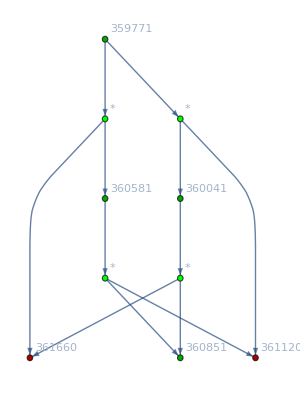
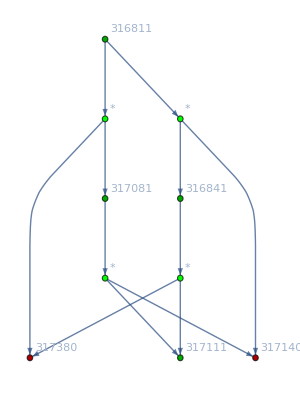
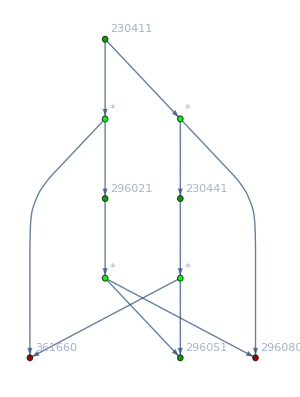
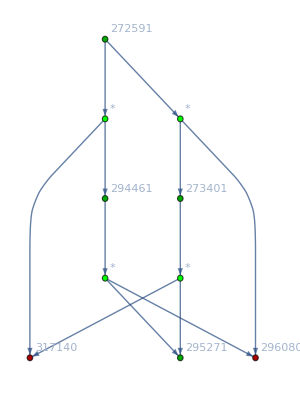
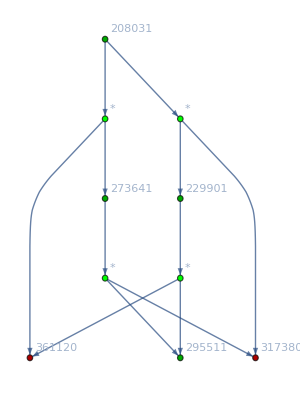

```mathematica
Table[DependencyGraph2[allGraphs5,k,RepGraph["C"]],{k,{alfaKey,betaKey,gammaKey,epsilonKey,deltaKey}}]
```

```mathematica
Graph[Fold[GraphUnion,Table[DependencyGraph3[allGraphs5,k,RepGraph["C"]],{k,{alfaKey,betaKey,gammaKey,epsilonKey,deltaKey}}]],VertexLabels->"Name"]
```

GraphUnion::graph: A graph object is expected at position 1 in ….

$Aborted[]

GraphUnion::graph: A graph object is expected at position 1 in ….

General::stop: Further output of GraphUnion::graph will be suppressed during this calculation.

$Aborted[]

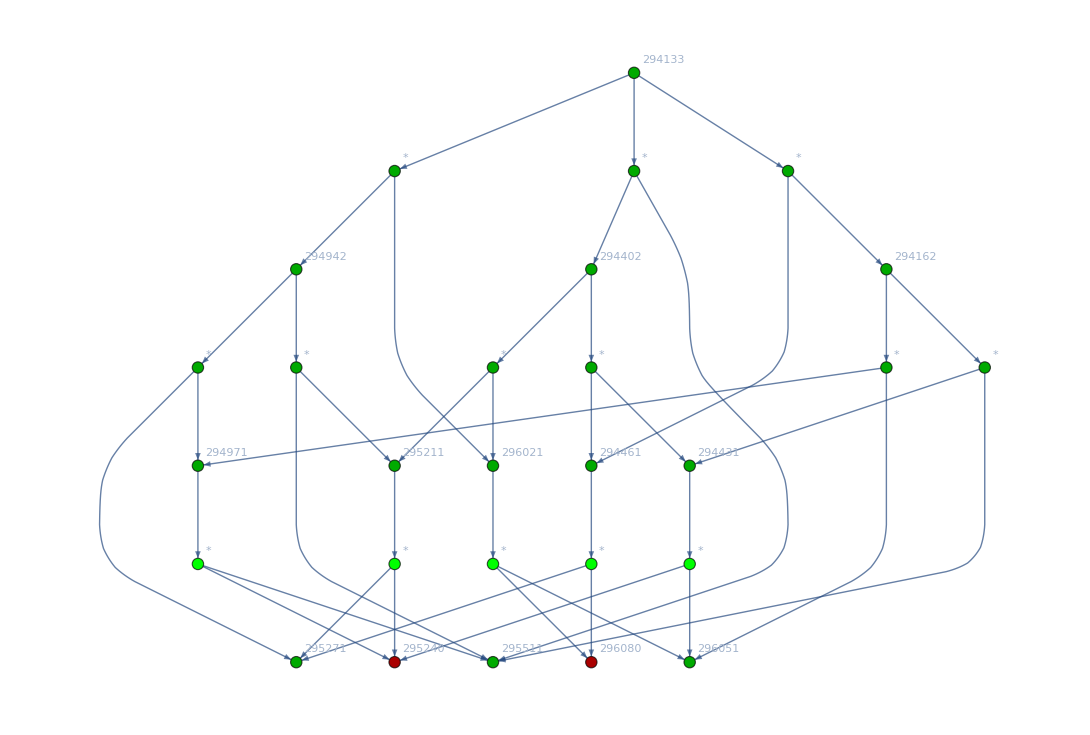

```mathematica
DependencyGraph2[allGraphs5,amigo1,RepGraph["C"]]
```

```mathematica
DependencyGraph3[assoc_,startKey_,rep_:{}]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={},currentColor},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
visited=Append[visited,currentKey];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
currentColor=ColourForKey[assoc,currentKey];
vertexColors=Append[vertexColors,currentKey->currentColor];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
ShowGraph5Least[currentKey]];
children=assoc[currentKey,"children"];
If[ToString[assoc[currentKey]["comp"]]≠"Equal",
Table[
Table[
If[True||!MemberQ[visited,child],
edges=Append[edges,currentKey->child];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
]
],
{Length[todo],Length[visited]}
];
Graph[
vertices,
DeleteDuplicates[edges],
VertexStyle->DeleteDuplicates[vertexColors], 
VertexLabels->DeleteDuplicates[vertexLabels],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->300
]
]
```

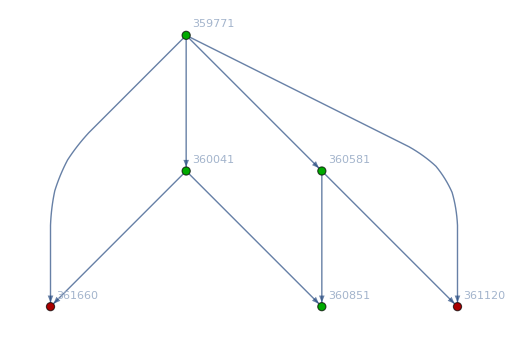

```mathematica
DependencyGraph3[allGraphs5,alfaKey,RepGraph["C"]]
```